## Input Data

```mathematica
PupRSB = {2.7125668477753084,1.6128992895387009,7.111527176871333,12.609880167484134,4.911953307642812,21.40778774210963,12.609880167484134,15.9090956858946,9.310821800213464,15.9090956858946,6.011735831960196,8.211012903577762,2.7125668477753084};
PupBSB = {11.51025669167044,12.609880167484134,15.9090956858946,19.208053514849173,29.105467984043372,25.80645577429066,26.906159381779936,25.80645577429066,20.307976051164427,18.10850830841342,14.8093666274799,13.709769145554757,11.51025669167044};

ωdet = -0.3
ωstep = 0.05
ωdat = Table[ωdet  + i ωstep,{i,0,12}];

freqapproxRSB = 9508.84;
freqapproxBSB = 8581.14;

dataRSB  = Transpose[{ωdat+ freqapproxRSB, PupRSB }];
dataBSB  = Transpose[{ωdat+ freqapproxBSB, PupBSB }];
```

-0.3

0.05

## Functions

```mathematica
Ω0approx = 0.295;
fitFunc[A_, Ω0_,ω_,ω0_] := A Ω0^2/(Ω0^2+(ω-ω0)^2) Sin[(√(Ω0^2+(ω-ω0)^2)π)/(2 Ω0)]^2;
fitRSB=FindFit[dataRSB,{fitFunc[A0,Ω0,ω,ω0] ,{ ω0>freqapproxRSB + ωdet , ω0 <freqapproxRSB + ωdet + 12ωstep}},{{A0,0},{Ω0,Ω0approx},{ω0,freqapproxRSB}},ω]
fitBSB =FindFit[dataBSB,{fitFunc[A0,Ω0,ω,ω0] ,{ ω0>freqapproxBSB + ωdet , ω0 <freqapproxBSB + ωdet + 12ωstep}},{{A0,0},{Ω0,Ω0approx},{ω0,freqapproxBSB}},ω]
```

FindFit::ivar: 1.26428×10^10 is not a valid variable.

FindFit[{{9508.54,2.71257},{9508.59,1.6129},{9508.64,7.11153},{9508.69,12.6099},{9508.74,4.91195},{9508.79,21.4078},{9508.84,12.6099},{9508.89,15.9091},{9508.94,9.31082},{9508.99,15.9091},{9509.04,6.01174},{9509.09,8.21101},{9509.14,2.71257}},{(A0 Ω0^2 Sin[(π √((-1.26428×10^10+ω)^2+Ω0^2))/(2 Ω0)]^2)/((-1.26428×10^10+ω)^2+Ω0^2),{True,False}},{{A0,0},{Ω0,0.295},{1.26428×10^10,9508.84}},ω]

FindFit::ivar: 1.26428×10^10 is not a valid variable.

FindFit[{{8580.84,11.5103},{8580.89,12.6099},{8580.94,15.9091},{8580.99,19.2081},{8581.04,29.1055},{8581.09,25.8065},{8581.14,26.9062},{8581.19,25.8065},{8581.24,20.308},{8581.29,18.1085},{8581.34,14.8094},{8581.39,13.7098},{8581.44,11.5103}},{(A0 Ω0^2 Sin[(π √((-1.26428×10^10+ω)^2+Ω0^2))/(2 Ω0)]^2)/((-1.26428×10^10+ω)^2+Ω0^2),{True,False}},{{A0,0},{Ω0,0.295},{1.26428×10^10,8581.14}},ω]

## Output

FindFit::ivar: 1.26428×10^10 is not a valid variable.

ReplaceAll::reps: {FindFit[{{9508.54,2.71257},{9508.59,1.6129},{9508.64,7.11153},{9508.69,12.6099},{9508.74,4.91195},{9508.79,21.4078},{9508.84,12.6099},{9508.89,15.9091},{9508.94,9.31082},{9508.99,15.9091},{9509.04,6.01174},{9509.09,8.21101},{9509.14,2.71257}},{(«1»)/(«1»),{«1»}},«1»,9508.54]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 1.26428×10^10 is not a valid variable.

ReplaceAll::reps: {FindFit[{{9508.54,2.71257},{9508.59,1.6129},{9508.64,7.11153},{9508.69,12.6099},{9508.74,4.91195},{9508.79,21.4078},{9508.84,12.6099},{9508.89,15.9091},{9508.94,9.31082},{9508.99,15.9091},{9509.04,6.01174},{9509.09,8.21101},{9509.14,2.71257}},{(«1»)/(«1»),{«1»}},«1»,9508.54]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 1.26428×10^10 is not a valid variable.

General::stop: Further output of FindFit::ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{9508.54,2.71257},{9508.59,1.6129},{9508.64,7.11153},{9508.69,12.6099},{9508.74,4.91195},{9508.79,21.4078},{9508.84,12.6099},{9508.89,15.9091},{9508.94,9.31082},{9508.99,15.9091},{9509.04,6.01174},{9509.09,8.21101},{9509.14,2.71257}},{(«1»)/(«1»),{«1»}},«1»,9508.55]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

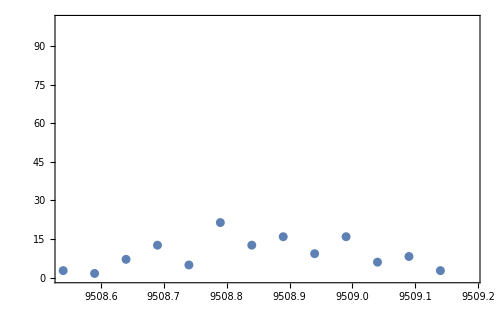

```mathematica
Show[ListPlot[dataRSB],
Plot[fitFunc[A0, Ω0, ω, ω0]/.fitRSB, {ω,freqapproxRSB + ωdet, freqapproxRSB + ωdet + 13ωstep}],
PlotRange-> {{freqapproxRSB + ωdet, freqapproxRSB + ωdet + 13ωstep},{0,100}},
Frame-> True, ImageSize-> 500]
```

FindFit::ivar: 1.26428×10^10 is not a valid variable.

ReplaceAll::reps: {FindFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 1.26428×10^10 is not a valid variable.

ReplaceAll::reps: {FindFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: 1.26428×10^10 is not a valid variable.

General::stop: Further output of FindFit::ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

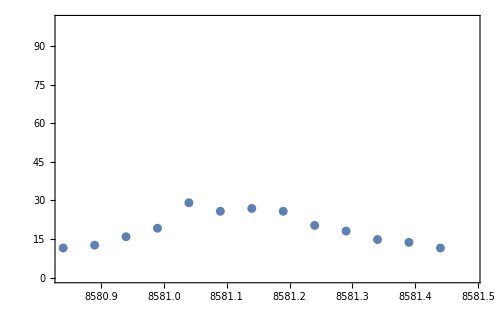

```mathematica
Show[ListPlot[dataBSB],
Plot[fitFunc[A0, Ω0, ω, ω0]/.fitBSB, {ω,freqapproxBSB + ωdet, freqapproxBSB + ωdet + 13ωstep}],
PlotRange-> {{freqapproxBSB + ωdet, freqapproxBSB + ωdet + 13ωstep},{0,100}},
Frame-> True, ImageSize-> 500]
```

## Final nbar

```mathematica
fitRSB = {A0-> Max[PupRSB]}
nbar = (A0/.fitRSB) / (A0/.fitBSB)
```

{A0→21.4078}

FindFit::ivar: 1.26428×10^10 is not a valid variable.

ReplaceAll::reps: {FindFit[{{8580.84,11.5103},{8580.89,12.6099},{8580.94,15.9091},{8580.99,19.2081},{8581.04,29.1055},{8581.09,25.8065},{8581.14,«19»},{8581.19,25.8065},{8581.24,20.308},{8581.29,18.1085},{8581.34,14.8094},{8581.39,13.7098},{8581.44,11.5103}},«3»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

21.4078/(A0/.FindFit[{{8580.84,11.5103},{8580.89,12.6099},{8580.94,15.9091},{8580.99,19.2081},{8581.04,29.1055},{8581.09,25.8065},{8581.14,26.9062},{8581.19,25.8065},{8581.24,20.308},{8581.29,18.1085},{8581.34,14.8094},{8581.39,13.7098},{8581.44,11.5103}},{(A0 Ω0^2 Sin[(π √((-1.26428×10^10+ω)^2+Ω0^2))/(2 Ω0)]^2)/((-1.26428×10^10+ω)^2+Ω0^2),{True,False}},{{A0,0},{Ω0,0.295},{1.26428×10^10,8581.14}},ω])

## Fit to nbar

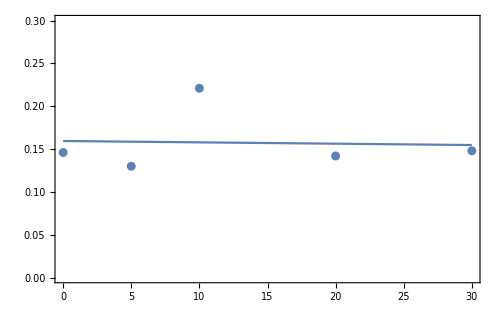

```mathematica
nbarData = {0.146, 0.130, 0.221, 0.142, 0.148};
timeData = {0, 5, 10, 20, 30};
heatingData = Transpose[{timeData, nbarData}];

heatingFit = FindFit[heatingData, x ndot + n0 ,{{ndot, 0.001}, {n0, 0.1}},x];

Show[ListPlot[heatingData],
Plot[(x ndot + n0)/.heatingFit, {x,0,30}],
PlotRange-> {{0, 30},{0,0.3}},
Frame-> True, ImageSize-> 500]
```